```mathematica
Needs["NDSolve`FEM`"]
```

ElementMesh[{{-10.,10.},{-10.,10.}},{TriangleElement[<20271>]}]

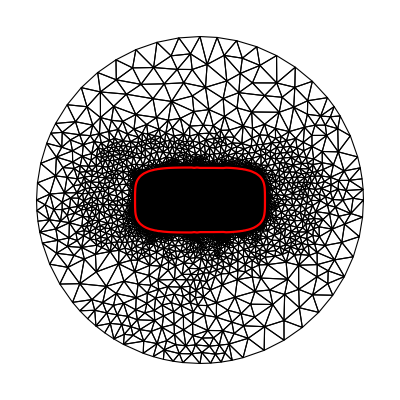

```mathematica
RefinedRegionFormula=x^4+(2y)^4;
f=Function[{vertices,area},Block[{x,y},{x,y}=Mean[vertices];If[RefinedRegionFormula≤250,area>0.003,If[RefinedRegionFormula≤2500,area>0.1,area>1]]]];
em=ToElementMesh[RegionUnion[Disk[{0,0},10]],MeshQualityGoal->"Maximal",MeshRefinementFunction->f]
Show[em["Wireframe"],ContourPlot[RefinedRegionFormula==250,{x,-10,10},{y,-10,10},ColorFunction->Hue]]
```

```mathematica
?Disk[{0,0},10]
```

Missing[UnknownSymbol,Disk[{0,0},10]]

```mathematica
?ToElementMesh
```

```mathematica
em["Wireframe"]
```

ToElementMesh[RegioUnion[Disk[{0,0},10],Rectangle[{0,0},{12,13}]]][Wireframe]

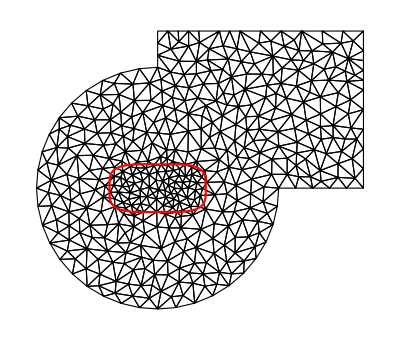

```mathematica
?Rectangle
```

```mathematica
Import["/Users/gustavomanzari/GitHub/Numerical-Simulation-for-NACA-Airfoil-with-Spalart-Allmaras-Turbulence-Model/NACAa63a108c.jpg"]
```

```mathematica
shape=-Graphics-;
```

```mathematica
dist=ColorNegate[LaplacianGaussianFilter[shape,80]];
ImageAdjust@dist
```

-Graphics-

```mathematica
data=Transpose[Reverse[-ImageData[dist]*(2*ImageData[shape]-1)]];
dataRange=Transpose[{{1, 1},Dimensions[data]}];
if=ListInterpolation[data,{dataRange[[1]]-MeandataRange[[1]],dataRange[[2]]-MeandataRange[[2]]},InterpolationOrder->1];
```

```mathematica
cf=Compile[{{c,_Real,2},{area,_Real,0}},
Block[{com,res},
com=Total[c]/Length[c];
res=If[area>Max[Abs[if[com[[1]],com[[2]]]],2.5],True,False];
res]
];
```

```mathematica
mesh=ToElementMesh[RegionUnion[Disk[{0,0},10],FullRegion[2]],{dataRange[[1]]-MeandataRange[[1]],dataRange[[2]]-MeandataRange[[2]]},MeshQualityGoal->"Maximal",MeshRefinementFunction->cf,"MeshElementType"->"TriangleElement"]
```

ElementMesh[{{-179.5,179.5},{-64.,64.}},{TriangleElement[<31405>]}]

```mathematica
?FullRegion
```

```mathematica
MeandataRange={Mean[dataRange[[1]]],Mean[dataRange[[2]]]}
```

{361/2,65}

{{-359/2,359/2},{-64,64}}

```mathematica
data
```

```mathematica
Transpose[{{1, 1},Dimensions[data][[1;;2]]}]
```

{{1,360},{1,129}}

```mathematica
Transpose[{{1, 1},Dimensions[data][[1;;2]]}]
```

{{1,360},{1,129}}

```mathematica
?ListInterpolation
```

```mathematica
coordsNACA={{1.,0.},{0.995,-0.00029},{0.99,-0.00059},{0.98,-0.00117},{0.97,-0.00176},{0.96,-0.00234},{0.95,-0.00292},{0.925,-0.00438},{0.9,-0.00584},{0.875,-0.00729},{0.85,-0.00874},{0.825,-0.01018},{0.8,-0.01167},{0.775,-0.01327},{0.75,-0.01492},{0.725,-0.01661},{0.7,-0.0183},{0.65,-0.02157},{0.6,-0.02459},{0.55,-0.02728},{0.5,-0.02957},{0.45,-0.0314},{0.4,-0.03269},{0.35,-0.0334},{0.3,-0.0335},{0.25,-0.03297},{0.2,-0.03183},{0.175,-0.03097},{0.15,-0.02989},{0.125,-0.02852},{0.1,-0.0268},{0.09,-0.02598},{0.08,-0.02506},{0.07,-0.02403},{0.06,-0.02286},{0.05,-0.02152},{0.04,-0.01996},{0.03,-0.01808},{0.02,-0.01569},{0.01,-0.01228},{0.005,-0.00959},{0.004,-0.00885},{0.003,-0.00796},{0.002,-0.00686},{0.001,-0.00531},{0.0008,-0.00489},{0.0006,-0.0044},{0.0004,-0.00379},{0.0002,-0.00277},{0.,0.},{0.,0.},{0.0002,0.00445},{0.0004,0.00549},{0.0006,0.00626},{0.0008,0.00687},{0.001,0.00741},{0.002,0.00943},{0.003,0.01091},{0.004,0.01212},{0.005,0.01315},{0.01,0.01695},{0.02,0.02192},{0.03,0.02539},{0.04,0.02807},{0.05,0.03024},{0.06,0.03206},{0.07,0.0336},{0.08,0.03493},{0.09,0.03608},{0.1,0.03709},{0.125,0.03911},{0.15,0.04062},{0.175,0.04173},{0.2,0.04255},{0.25,0.04351},{0.3,0.04385},{0.35,0.04362},{0.4,0.04293},{0.45,0.04176},{0.5,0.04015},{0.55,0.0381},{0.6,0.03559},{0.65,0.03258},{0.7,0.02906},{0.725,0.0272},{0.75,0.0252},{0.775,0.0231},{0.8,0.0209},{0.825,0.0187},{0.85,0.0164},{0.875,0.0141},{0.9,0.012},{0.925,0.0101},{0.95,0.0086},{0.96,0.008},{0.97,0.0076},{0.98,0.0073},{0.99,0.0071},{0.995,0.007},{1.,0}};
```

```mathematica
ToBoundaryMesh[Disk[{0,0},10],LineElement[coordsNACA]]
```

LineElement::femdmi: Mesh element type LineElement does not match incidents {{1.,0.},{0.995,-0.00029},{0.99,-0.00059},{0.98,-0.00117},{0.97,-0.00176},{0.96,-0.00234},{0.95,-0.00292},{0.925,-0.00438},{0.9,-0.00584},{0.875,-0.00729},«90»}.

```mathematica
bmesh=ToBoundaryMesh[ImplicitRegion[x^2+y^2≤1&&coordsNACA,{x,y}]];
bmesh["Wireframe"]
```

ImplicitRegion::bcond: x^2+y^2≤1&&{{1.,0.},{0.995,-0.00029},{0.99,-0.00059},{0.98,-0.00117},{0.97,-0.00176},{0.96,-0.00234},{0.95,-0.00292},{0.925,-0.00438},{0.9,-0.00584},{0.875,-0.00729},«90»} should be a Boolean combination of equations, inequalities, and Element statements.

ToBoundaryMesh[ImplicitRegion[x^2+y^2≤1&&coordsNACA,{x,y}]][Wireframe]

```mathematica
ToElementMesh[RegionDifference[Disk[{0,0},10],Polygon[NACA23012]]]
```

```mathematica
Polygon[coordsNACA]
```

```mathematica
TeElementMesh[Polygon[…]]
```

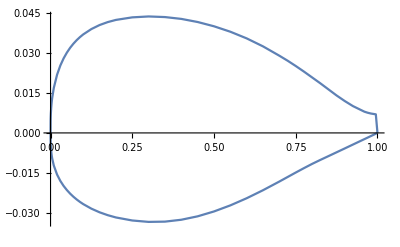

```mathematica
ListLinePlot[{{1,0},{0.995,-0.00029},{0.99,-0.00059},{0.98,-0.00117},{0.97,-0.00176},{0.96,-0.00234},{0.95,-0.00292},{0.925,-0.00438},{0.9,-0.00584},{0.875,-0.00729},{0.85,-0.00874},{0.825,-0.01018},{0.8,-0.01167},{0.775,-0.01327},{0.75,-0.01492},{0.725,-0.01661},{0.7,-0.0183},{0.65,-0.02157},{0.6,-0.02459},{0.55,-0.02728},{0.5,-0.02957},{0.45,-0.0314},{0.4,-0.03269},{0.35,-0.0334},{0.3,-0.0335},{0.25,-0.03297},{0.2,-0.03183},{0.175,-0.03097},{0.15,-0.02989},{0.125,-0.02852},{0.1,-0.0268},{0.09,-0.02598},{0.08,-0.02506},{0.07,-0.02403},{0.06,-0.02286},{0.05,-0.02152},{0.04,-0.01996},{0.03,-0.01808},{0.02,-0.01569},{0.01,-0.01228},{0.005,-0.00959},{0.004,-0.00885},{0.003,-0.00796},{0.002,-0.00686},{0.001,-0.00531},{0.0008,-0.00489},{0.0006,-0.0044},{0.0004,-0.00379},{0.0002,-0.00277},{0.,0.},{0.,0.},{0.0002,0.00445},{0.0004,0.00549},{0.0006,0.00626},{0.0008,0.00687},{0.001,0.00741},{0.002,0.00943},{0.003,0.01091},{0.004,0.01212},{0.005,0.01315},{0.01,0.01695},{0.02,0.02192},{0.03,0.02539},{0.04,0.02807},{0.05,0.03024},{0.06,0.03206},{0.07,0.0336},{0.08,0.03493},{0.09,0.03608},{0.1,0.03709},{0.125,0.03911},{0.15,0.04062},{0.175,0.04173},{0.2,0.04255},{0.25,0.04351},{0.3,0.04385},{0.35,0.04362},{0.4,0.04293},{0.45,0.04176},{0.5,0.04015},{0.55,0.0381},{0.6,0.03559},{0.65,0.03258},{0.7,0.02906},{0.725,0.0272},{0.75,0.0252},{0.775,0.0231},{0.8,0.0209},{0.825,0.0187},{0.85,0.0164},{0.875,0.0141},{0.9,0.012},{0.925,0.0101},{0.95,0.0086},{0.96,0.008},{0.97,0.0076},{0.98,0.0073},{0.99,0.0071},{0.995,0.007},{1.,0}}]
```

```mathematica
NACA23012=Import["/Users/gustavomanzari/GitHub/Numerical-Simulation-for-NACA-Airfoil-with-Spalart-Allmaras-Turbulence-Model/Airfoil Data/naca23012.dat"][[2;;-1]]
```

```mathematica
{{1.00003,0.00},{0.9973,0.0017},{0.98914,0.00302},{0.97563,0.00518},{0.95693,0.00812},{0.93324,0.01176},{0.90482,0.01602},{0.87197,0.02079},{0.83506,0.02597},{0.79449,0.03145},{0.7507,0.03712},{0.70417,0.04285},{0.65541,0.04854},{0.60496,0.05405},{0.55335,0.05924},{0.50117,0.06397},{0.44897,0.06811},{0.39733,0.0715},{0.34681,0.07402},{0.29796,0.07554},{0.25131,0.07597},{0.20738,0.07524},{0.16604,0.0732},{0.12732,0.06915},{0.0923,0.06265},{0.06203,0.05382},{0.0373,0.04324},{0.01865,0.03176},{0.00628,0.0203},{0.00015,0.00956},{0.,0.},{0.00533,-0.00792},{0.01557,-0.01401},{0.03029,-0.0187},{0.04915,-0.02248},{0.07195,-0.02586},{0.09868,-0.02922},{0.12954,-0.03282},{0.16483,-0.0366},{0.20483,-0.04016},{0.24869,-0.04283},{0.29531,-0.04446},{0.34418,-0.0451},{0.39476,-0.04482},{0.4465,-0.04371},{0.49883,-0.04188},{0.55117,-0.03945},{0.60296,-0.03655},{0.6536,-0.03327},{0.70257,-0.02975},{0.7493,-0.02607},{0.7933,-0.02235},{0.83407,-0.01866},{0.87118,-0.01512},{0.9042,-0.0118},{0.93279,-0.0088},{0.95661,-0.00621},{0.97543,-0.0041},{0.98901,-0.00254},{0.99722,-0.00158},{0.99997,-0.00}}
```

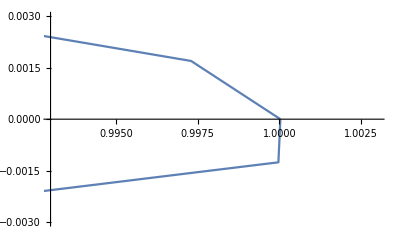

```mathematica
NACA23012={{1.00003,0},{0.9973,0.0017},{0.98914,0.00302},{0.97563,0.00518},{0.95693,0.00812},{0.93324,0.01176},{0.90482,0.01602},{0.87197,0.02079},{0.83506,0.02597},{0.79449,0.03145},{0.7507,0.03712},{0.70417,0.04285},{0.65541,0.04854},{0.60496,0.05405},{0.55335,0.05924},{0.50117,0.06397},{0.44897,0.06811},{0.39733,0.0715},{0.34681,0.07402},{0.29796,0.07554},{0.25131,0.07597},{0.20738,0.07524},{0.16604,0.0732},{0.12732,0.06915},{0.0923,0.06265},{0.06203,0.05382},{0.0373,0.04324},{0.01865,0.03176},{0.00628,0.0203},{0.00015,0.00956},{0.,0.},{0.00533,-0.00792},{0.01557,-0.01401},{0.03029,-0.0187},{0.04915,-0.02248},{0.07195,-0.02586},{0.09868,-0.02922},{0.12954,-0.03282},{0.16483,-0.0366},{0.20483,-0.04016},{0.24869,-0.04283},{0.29531,-0.04446},{0.34418,-0.0451},{0.39476,-0.04482},{0.4465,-0.04371},{0.49883,-0.04188},{0.55117,-0.03945},{0.60296,-0.03655},{0.6536,-0.03327},{0.70257,-0.02975},{0.7493,-0.02607},{0.7933,-0.02235},{0.83407,-0.01866},{0.87118,-0.01512},{0.9042,-0.0118},{0.93279,-0.0088},{0.95661,-0.00621},{0.97543,-0.0041},{0.98901,-0.00254},{0.99722,-0.00158},{0.99997,-0.00126},{1.00003,0}};
ListLinePlot[NACA23012,PlotRange->{{0.993,1.003},{-0.003,0.003}}]
```

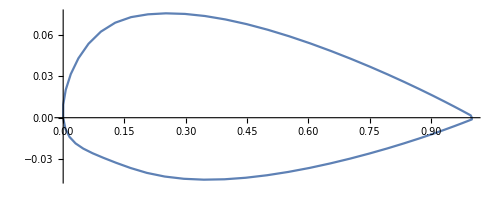

```mathematica
ListLinePlot[NACA23012,AspectRatio->Automatic]
```